## Graphical representation

```mathematica
ClearAll["Global`*"]
```

```mathematica
spin0={7.5,9.5,11.5,13.5,15.5,17.5,19.5,21.5,23.5,25.5,27.5};
spin1={8.5,10.5,12.5,14.5,16.5};
spin2={9.5,11.5,13.5,15.5};
band1exp={0.3729,1.0327,1.887,2.8867,3.9623,4.806,5.6403,6.5225,7.4449,8.4019,9.4069};
band1th={0.6489231303332899,1.3416115046837764,2.0786652448783793,2.860331759974865,3.6867336223178806,4.557939039239063,5.473989176901558,6.434910428394987,7.440720528273122,8.491431849871653,9.587053296875014};
band2exp={0.7466,1.4731,2.2688,3.2245,4.3362};
band2th={0.9897459594242473,1.7045729395035516,2.4639124739781493,3.26793566451142,4.116732866147538};
band3exp={1.1971,2.0237,2.7875,3.7965};
band3th={1.257638840232143,2.0279506060426935,2.841912394589692,3.7000375108632677};
```

## wobbling frequency

```mathematica
spiner={7.5,9.5,11.5,13.5,15.5,17.5,19.5,21.5,23.5,25.5,27.5,29.5,31.5,33.5,35.5,37.5,39.5,41.5,43.5,45.5,47.5,49.5,51.5,53.5,55.5};
omega1={0.2396239446711212,0.29577533916945387,0.3507698249065808,0.4051022199980349,0.45901766913311104,0.5126525869750805,0.5660893058502366,0.6193806119378229,0.6725619743453888,0.7256581397443025,0.7786869155034409,0.8316614512977195,0.8845916733135273,0.9374852177908956,0.9903480570838875,1.0431849305052718,1.095999647607474,1.1487953059735725,1.2015744504198753,1.2543391912382602,1.3070912932858032,1.3598322439878638,1.412563305863929,1.465285557540632,1.517999926095503};
omega2={0.11407245996580151,0.18169741807021014,0.24188505482406933,0.29919011938775714,0.3550241522460023,0.40999464904253985,0.464411507952753,0.5184508638001228,0.5722207391170504,0.625791267058859,0.6792100527347249,0.732510588417634,0.7857171439357932,0.8388477481433153,0.8919160803394978,0.9449327111711742,0.997905940544197,1.0508423777400107,1.1037473519510095,1.1566252084936448,1.2094795262591025,1.2623132798379064,1.3151289620980031,1.3679286780466928,1.4207142175402623};
```

```mathematica
band1plot=ListPlot[{Table[{spin0[[i]],band1exp[[i]]},{i,1,Length[spin0]}],Table[{spin0[[i]],band1th[[i]]},{i,1,Length[spin0]}]},FrameStyle->Directive[Black,Thick],Frame->True,Axes->False,PlotStyle->{Black,{Red,Thick}},Joined->{False,True},PlotLegends->Placed[{"Exp","Th"},{0.25,0.75}],LabelStyle->{22,Black,Bold,FontFamily->"Times New Roman"},PlotRange->Automatic,PlotMarkers->{{Automatic,11},None},AspectRatio->0.7,Epilog->{Inset[Framed[Style["^135Pr",20,Italic,Black,FontFamily->"Times New Roman"],Background->None,FrameStyle->White],Scaled[{.82,.30}]],Inset[Framed[Style["1^st band" ,20,Italic,Black,FontFamily->"Times New Roman"],Background->None,FrameStyle->White],Scaled[{.78,.18}]]},FrameLabel->{"I [ℏ}","E_I [MeV]"}];
```

```mathematica
band2plot=ListPlot[{Table[{spin1[[i]],band2exp[[i]]},{i,1,Length[spin1]}],Table[{spin1[[i]],band2th[[i]]},{i,1,Length[spin1]}]},FrameStyle->Directive[Black,Thick],Frame->True,Axes->False,PlotStyle->{Black,{Red,Thick}},Joined->{False,True},PlotLegends->Placed[{"Exp","Th"},{0.25,0.75}],LabelStyle->{22,Black,Bold,FontFamily->"Times New Roman"},PlotRange->Automatic,PlotMarkers->{{Automatic,11},None},AspectRatio->0.7,Epilog->{Inset[Framed[Style["^135Pr",20,Italic,Black,FontFamily->"Times New Roman"],Background->None,FrameStyle->White],Scaled[{.82,.30}]],Inset[Framed[Style["2^nd band" ,20,Italic,Black,FontFamily->"Times New Roman"],Background->None,FrameStyle->White],Scaled[{.78,.18}]]},FrameLabel->{"I [ℏ}","E_I [MeV]"}];
```

```mathematica
band3plot=ListPlot[{Table[{spin2[[i]],band3exp[[i]]},{i,1,Length[spin2]}],Table[{spin2[[i]],band3th[[i]]},{i,1,Length[spin2]}]},FrameStyle->Directive[Black,Thick],Frame->True,Axes->False,PlotStyle->{Black,{Red,Thick}},Joined->{False,True},PlotLegends->Placed[{"Exp","Th"},{0.25,0.75}],LabelStyle->{22,Black,Bold,FontFamily->"Times New Roman"},PlotRange->Automatic,PlotMarkers->{{Automatic,11},None},AspectRatio->0.7,Epilog->{Inset[Framed[Style["^135Pr",20,Italic,Black,FontFamily->"Times New Roman"],Background->None,FrameStyle->White],Scaled[{.82,.30}]],Inset[Framed[Style["3^rd band" ,20,Italic,Black,FontFamily->"Times New Roman"],Background->None,FrameStyle->White],Scaled[{.78,.18}]]},FrameLabel->{"I [ℏ}","E_I [MeV]"}];
```

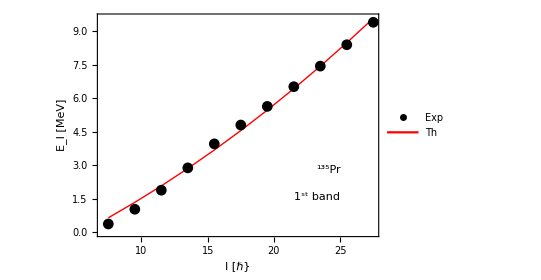

```mathematica
Show[band1plot]
```

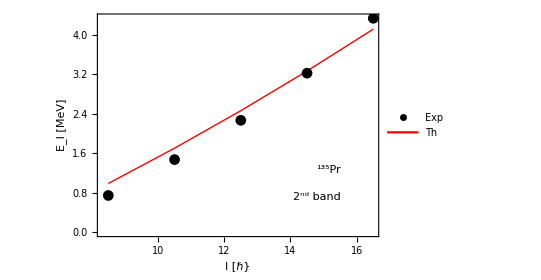

```mathematica
Show[band2plot]
```

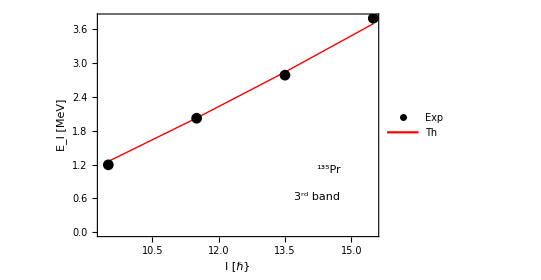

```mathematica
Show[band3plot]
```

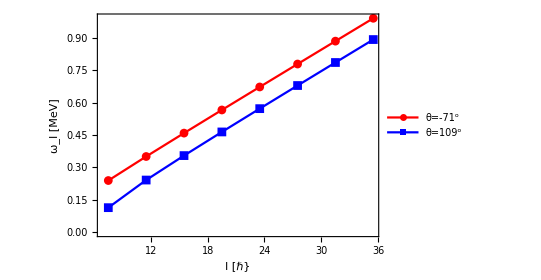

```mathematica
wobblingfreqs=ListPlot[{Table[{spiner[[i]],omega1[[i]]},{i,1,15,2}],Table[{spiner[[i]],omega2[[i]]},{i,1,15,2}]},FrameStyle->Directive[Black,Thick],Frame->True,Axes->False,PlotStyle->{Red,Blue},PlotLegends->Placed[{"θ=-71^o","θ=109^o"},{0.25,0.75}],LabelStyle->{22,Black,Bold,FontFamily->"Times New Roman"},PlotMarkers->{Automatic,9},AspectRatio->0.7,Joined->True,PlotRange->All,FrameLabel->{"I [ℏ}","ω_I [MeV]"}]
```